# Can We Calculate a Transformer by Hand?

## A tiny transformer language model, worked entirely by hand — from "run casing" to a probability for "shoe"

Modern language models contain billions of parameters and perform trillions of arithmetic operations per response. Nobody reproduces that by hand, and nobody needs to — but the arithmetic itself is not exotic. It is addition, multiplication, exponentials, and logarithms, arranged in a particular pattern called a transformer.

This notebook shrinks that pattern down until every number fits on a sheet of paper. I use a vocabulary of 6 words, sequences of 2 tokens, and an embedding dimension of 2. The whole model has a few dozen parameters. Every matrix multiplication, every softmax, every gradient below can be checked with a calculator.

The example is a drilling/completions phrase: given the two-word input "run casing", the model should predict that the next word is "shoe" (as in a casing shoe). This is a toy transformer LANGUAGE model — not an LLM, and not any kind of reproduction of ChatGPT or similar production systems. Its only job is to make the mechanics of attention, softmax, loss, and gradient descent completely visible.

### The shape of the calculation

Here is the full pipeline we are about to compute, start to finish. Every arrow below corresponds to a section of this notebook and an explicit matrix or vector calculation.

"run casing"
    ↓
Token IDs                    (Section 2)
    ↓
Embeddings                   (Section 3)
    ↓
Q, K, V                      (Section 4)
    ↓
Scaled dot-product attention  (Sections 5-8)
    ↓
Output representation        (Section 8)
    ↓
Logits                       (Section 9)
    ↓
Softmax probabilities        (Section 10)
    ↓
Prediction: "shoe"?
    ↓
Cross-entropy loss           (Section 11)
    ↓
Gradient                     (Section 12)
    ↓
Weight update                (Section 13)
    ↓
New prediction                (Section 14)

### What this notebook is — and is not

This is a transformer: the same attention-then-project pattern used by real language models, reduced to a size a person can compute by hand. It is a language model in the narrow technical sense of Section 1 below: something that assigns probabilities to "what word comes next". It is not an LLM (a large language model with billions of parameters trained on enormous text corpora), and it is not ChatGPT, Claude, or any production system. Treat every number in this notebook as belonging to a teaching-sized toy, not a scaled-down copy of a real product.

### What we left out, and why that is fine here

LayerNorm — real transformers rescale activations between steps to keep training stable across many layers. With one block and tens of parameters, there is nothing to destabilize.

Residual (skip) connections — these help gradients flow through many stacked layers. We only have one layer, so there is no long path for a gradient to vanish along.

Dropout — a regularizer that fights overfitting on large datasets. We have exactly one training example, so overfitting is not the concern; transparency is.

Multi-head attention — real models run several attention computations in parallel and combine them. One head already shows the complete mechanism; a second head would only duplicate arithmetic without adding a new idea.

A large feed-forward network inside the block — omitted so that the output projection (Section 9) is the only place logits are produced, keeping the path from attention output to prediction short and traceable.

Positional encodings — with only 2 positions and a causal mask that already distinguishes "first token" from "second token", an explicit position signal would add notation without adding insight.

Every one of these choices trades realism for transparency. Section 16 returns to this trade-off explicitly.

## 1. The Prediction Problem

Given the two-word phrase:

"run casing"

we want the model to predict the single most likely next word. In this drilling/completions example, the correct next word is:

"shoe"

(as in a casing shoe, the equipment run on the bottom of a casing string).

In plain language, a language model's job is to compute:

P(next token | previous tokens)

— read as "the probability of the next token, given the tokens that came before it." The model does not know English, drilling engineering, or anything else. It only manipulates numbers derived from the input tokens, and those numbers happen to be arranged so that, after training, the right answer gets a high probability and everything else gets a low one. The rest of this notebook computes that probability distribution for "run casing" explicitly, one arithmetic step at a time, then shows how a single training update changes it.

## 2. Vocabulary and Token IDs

Computers do not work with words directly. The first step of any language model is to fix a vocabulary — a finite list of tokens the model knows about — and give every token an ID number (its position in the list). Any text the model sees must be built out of these tokens; anything outside the vocabulary simply cannot be represented.

Our vocabulary has 6 tokens: a beginning-of-sequence marker, three drilling-related words, one more drilling-related word, and an end-of-sequence marker.

```mathematica
Vocabulary = {"<BOS>", "run", "casing", "shoe", "cement", "<EOS>"};
Grid[Prepend[Transpose[{Vocabulary, Range[Length[Vocabulary]]}], {"Token", "Token ID"}],
  Frame -> All, Background -> {None, {LightGray, None}}]
```

Token | Token ID
<BOS> | 1
run | 2
casing | 3
shoe | 4
cement | 5
<EOS> | 6

Our input phrase "run casing" is a sequence of two tokens. Looking up each word's position in the list above turns the phrase into a list of token IDs:

```mathematica
inputTokens = {"run", "casing"};
tokenIDs = Flatten[Position[Vocabulary, #] & /@ inputTokens]
```

{2,3}

So "run casing" becomes {2, 3}: "run" is token 2 and "casing" is token 3. From this point on, the model never sees the words "run" or "casing" again — only the numbers 2 and 3, and (next) the vectors those numbers point to.

## 3. Embedding Lookup

A token ID like 2 is just a label — it carries no information about meaning or similarity between words. An embedding replaces each token ID with a vector of numbers (here, a vector of length 2) that the model can actually do arithmetic with. In a real model these vectors are learned from data and have hundreds of dimensions; here we fix them by hand, with dimension 2, so every coordinate can be inspected directly.

Below is the full embedding table: one row per vocabulary token, one column per embedding dimension.

```mathematica
EmbeddingMatrix = {
  {0, 0},   (* <BOS>  *)
  {1, 0},   (* run    *)
  {0, 1},   (* casing *)
  {1, 1},   (* shoe   *)
  {-1, 1},  (* cement *)
  {0, -1}   (* <EOS>  *)
};
Grid[Prepend[Transpose[{Vocabulary, EmbeddingMatrix}], {"Token", "Embedding"}],
  Frame -> All, Background -> {None, {LightGray, None}}]
```

Token | Embedding
<BOS> | {0,0}
run | {1,0}
casing | {0,1}
shoe | {1,1}
cement | {-1,1}
<EOS> | {0,-1}

"run" is deliberately set to {1, 0} and "casing" to {0, 1} — the two simplest possible distinct vectors in 2 dimensions. Selecting the rows for our input tokens {2, 3} builds the input matrix X: row 1 is the embedding of position 1 ("run"), row 2 is the embedding of position 2 ("casing"), and the 2 columns are the 2 embedding dimensions.

```mathematica
X = EmbeddingMatrix[[tokenIDs]];
MatrixForm[X]
```

(1 | 0
0 | 1)

```mathematica
Dimensions[X]
```

{2,2}

X is 2×2: 2 rows because our sequence has 2 tokens, 2 columns because our embedding dimension is 2. Because "run" and "casing" happen to be the two standard unit vectors, X is exactly the 2×2 identity matrix — a convenient coincidence that will make the next multiplications easy to check by hand, without changing what the multiplication means.

## 4. Query, Key, and Value Matrices

Attention compares positions to each other using three vectors derived from each position's embedding, called the query, key, and value. These are just names for the results of three ordinary matrix multiplications — there is no decision-making or comparison happening yet, only arithmetic that sets up the comparison in Section 5.

We fix three 2×2 weight matrices, WQ, WK, WV, by hand:

```mathematica
WQ = {{1, 0}, {1, 1}};
WK = {{1, 1}, {0, 1}};
WV = {{1, 0}, {0, 1}};
Row[{MatrixForm[WQ], "      ", MatrixForm[WK], "      ", MatrixForm[WV]}]
```

(1 | 0
1 | 1)      (1 | 1
0 | 1)      (1 | 0
0 | 1)

Query Q = X . WQ. Each row of Q is a row of X (a token's embedding) multiplied against the columns of WQ, entry-by-entry sum of products — ordinary matrix multiplication:

```mathematica
Q = X.WQ;
Row[{MatrixForm[X], "   .   ", MatrixForm[WQ], "   =   ", MatrixForm[Q]}]
```

(1 | 0
0 | 1)   .   (1 | 0
1 | 1)   =   (1 | 0
1 | 1)

Key K = X . WK, computed the same way:

```mathematica
K = X.WK;
Row[{MatrixForm[X], "   .   ", MatrixForm[WK], "   =   ", MatrixForm[K]}]
```

(1 | 0
0 | 1)   .   (1 | 1
0 | 1)   =   (1 | 1
0 | 1)

Value V = X . WV, computed the same way:

```mathematica
V = X.WV;
Row[{MatrixForm[X], "   .   ", MatrixForm[WV], "   =   ", MatrixForm[V]}]
```

(1 | 0
0 | 1)   .   (1 | 0
0 | 1)   =   (1 | 0
0 | 1)

Because X is the identity matrix (Section 3), each product above equals the corresponding weight matrix exactly (Q = WQ, K = WK, V = WV). You can verify this by hand: row 1 of X, {1,0}, times WQ picks out row 1 of WQ; row 2, {0,1}, picks out row 2. With a less convenient X the arithmetic is the same, just less obviously so.

## 5. Attention Scores

To measure how much position 2 should attend to position 1 (and to itself), we compare Q to K using a matrix product: Q . Transpose[K]. Each entry (i, j) of the result is the dot product of query i with key j — a single number summarizing how well they align.

```mathematica
rawScores = Q.Transpose[K];
Row[{MatrixForm[Q], "   .   ", MatrixForm[Transpose[K]], "   =   ", MatrixForm[rawScores]}]
```

(1 | 0
1 | 1)   .   (1 | 0
1 | 1)   =   (1 | 0
2 | 1)

Before using these numbers, we scale them down by Sqrt[d], where d = 2 is the embedding dimension. Why: as d grows, dot products of random vectors tend to grow larger in magnitude purely because more terms are being added up, which would push the softmax in Section 7 toward extremely peaked (near one-hot) outputs and make training unstable. Dividing by Sqrt[d] keeps the scores in a stable, comparable range regardless of dimension.

```mathematica
d = 2;
scaledScores = N[rawScores/Sqrt[d]];
MatrixForm[scaledScores]
```

(0.707107 | 0.
1.41421 | 0.707107)

## 6. Causal Mask

This is a next-token predictor: for every position, we ask it to predict the token that comes after that position. If position 1 ("run") were allowed to look at position 2 ("casing") while trying to predict what comes after "run", it would effectively be allowed to see part of the very continuation it is supposed to predict — not a fair test, and not how the model will be used at inference time, one token at a time.

A causal mask enforces this: position i may attend only to positions j ≤ i. We implement the mask by replacing every disallowed (future) entry with -∞, so that after the softmax in Section 7 those positions receive exactly zero attention weight.

```mathematica
maskedScores = {
  {scaledScores[[1, 1]], -Infinity},        (* position 1 ("run"): position 2 is masked *)
  {scaledScores[[2, 1]], scaledScores[[2, 2]]}  (* position 2 ("casing"): both positions allowed *)
};
MatrixForm[maskedScores]
```

(0.707107 | -∞
1.41421 | 0.707107)

Compare this to the unmasked scaledScores above: only the top-right entry changed, from a finite number to -∞. That single entry is exactly the score for "position 1 attending to position 2" — the one comparison a causal, left-to-right model is never allowed to make. Position 2 keeps both of its entries, because when predicting the token after "casing", the model is entitled to use everything up to and including "casing".

## 7. Softmax

Attention scores need to become a probability distribution — non-negative numbers that sum to 1 — so they can be used as weights in Section 8. Softmax does this:

Softmax[z_i] = Exp[z_i] / Sum[Exp[z_j], {j}]

Every score is exponentiated (so all results are positive), then divided by the sum of all the exponentials in that row (so the row sums to exactly 1). Let's do this by hand for row 2 (the "casing" row), the one with two real numbers to compare:

```mathematica
row2 = maskedScores[[2]];
exps = Exp[row2]
```

{4.11325,2.02811}

```mathematica
sumExps = Total[exps]
```

6.14137

```mathematica
softmaxRow2 = exps/sumExps
```

{0.669762,0.330238}

```mathematica
Total[softmaxRow2]
```

1.

The two exponentials are ~4.113 and ~2.028; dividing each by their sum ~6.141 gives probabilities ~0.670 and ~0.330, which do sum to 1 (up to floating-point rounding). Now apply the same formula, row by row, to the whole masked score matrix (row 1 is trivial: exp[x]/exp[x] = 1 for the only allowed entry, and 0 for the masked one):

```mathematica
SoftmaxRow[row_] := Module[{finite, m, ex},
   finite = Select[row, # > -Infinity &];
   m = Max[finite];
   ex = If[# > -Infinity, Exp[# - m], 0] & /@ row;
   ex/Total[ex]
];
attentionWeights = SoftmaxRow /@ maskedScores;
MatrixForm[attentionWeights]
```

(1. | 0.
0.669762 | 0.330238)

```mathematica
Total /@ attentionWeights
```

{1.,1.}

Both rows sum to 1, confirming attentionWeights is a valid pair of probability distributions. Row 1 is {1, 0}: position 1 puts all of its attention on itself, because the causal mask left it no other choice. Row 2 is approximately {0.670, 0.330}: position 2 splits its attention mostly onto position 1 ("run"), with some weight on itself.

## 8. Weighted Values

Attention weights tell us how much to blend the value vectors of each position. The blend itself is one more matrix multiplication:

AttentionOutput = AttentionWeights . V

```mathematica
attentionOutput = attentionWeights.V;
Row[{MatrixForm[attentionWeights], "   .   ", MatrixForm[V], "   =   ", MatrixForm[attentionOutput]}]
```

(1. | 0.
0.669762 | 0.330238)   .   (1 | 0
0 | 1)   =   (1. | 0.
0.669762 | 0.330238)

Row 1 of the result equals V's row 1 exactly ("run"'s own value vector), since row 1 of attentionWeights was {1,0}. Row 2 is a genuine blend: about 67% of V's row 1 plus 33% of V's row 2. This row — the representation built at position 2, after mixing in information from position 1 under the causal mask — is what we use to predict the token that comes after "casing":

```mathematica
h = attentionOutput[[2]]
```

{0.669762,0.330238}

## 9. Output Projection and Logits

h is a length-2 vector, but we need a score for every one of the 6 vocabulary tokens. The output projection matrix WOut (2 rows × 6 columns, one column per vocabulary token) does that conversion:

Logits = h . WOut

```mathematica
WOut = {
  {0, 1, 0,  1, -1,  0},
  {0, 0, 1, -1,  0, -1}
};
MatrixForm[WOut]
```

(0 | 1 | 0 | 1 | -1 | 0
0 | 0 | 1 | -1 | 0 | -1)

```mathematica
logits = h.WOut;
Grid[Prepend[Transpose[{Vocabulary, N[logits, 4]}], {"Token", "Logit"}],
  Frame -> All, Background -> {None, {LightGray, None}}]
```

Token | Logit
<BOS> | 0.
run | 0.669762
casing | 0.330238
shoe | 0.339523
cement | -0.669762
<EOS> | -0.330238

These are logits, not probabilities: they can be negative (cement, <EOS>), they do not sum to 1, and by themselves they only rank tokens relative to each other. "shoe" and "run" currently have the two largest logits, with "shoe" barely behind. The next section turns these into an actual probability distribution.

## 10. Next-Token Probabilities

We apply the same softmax formula from Section 7, this time to all 6 logits at once:

```mathematica
Softmax2[z_] := Module[{m = Max[z], ex}, ex = Exp[z - m]; ex/Total[ex]];
probabilities = Softmax2[logits];
Grid[Prepend[Transpose[{Vocabulary, N[logits, 4], N[probabilities, 4]}],
   {"Token", "Logit", "Probability"}], Frame -> All, Background -> {None, {LightGray, None}}]
```

Token | Logit | Probability
<BOS> | 0. | 0.143268
run | 0.669762 | 0.279913
casing | 0.330238 | 0.199329
shoe | 0.339523 | 0.201188
cement | -0.669762 | 0.0733289
<EOS> | -0.330238 | 0.102974

```mathematica
Total[probabilities]
```

1.

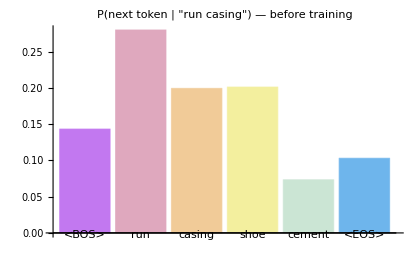

```mathematica
BarChart[probabilities, ChartLabels -> Vocabulary, ChartStyle -> "Pastel",
  PlotLabel -> "P(next token | \"run casing\") — before training", ImageSize -> 420]
```

```mathematica
targetIndex = First[Flatten[Position[Vocabulary, "shoe"]]];
predictedIndex = First[Ordering[probabilities, -1]];
{"target" -> Vocabulary[[targetIndex]], "predicted (highest probability)" -> Vocabulary[[predictedIndex]]}
```

{target→shoe,predicted (highest probability)→run}

Before any training, the model's highest-probability guess is "run" (~28.0%), not the correct answer "shoe" (~20.1%, third-highest). That mismatch between prediction and target is exactly what training will correct in Sections 11-14.

## 11. Cross-Entropy Loss

We need a single number that measures how wrong this prediction was, given that the true next token is "shoe". Cross-entropy loss for a single example is:

Loss = -Log[P(correct token)]

Plain-language reading: if the model had assigned probability 1 to the correct token, -Log[1] = 0 — no loss, a perfect prediction. As the assigned probability shrinks toward 0, -Log[p] grows without bound — a heavy penalty for confidently ruling out the right answer. It is not a distance or an error bar; it is a measure of "how surprised the model should be" about the true answer, in the specific sense used throughout information theory and statistics.

```mathematica
pShoe = probabilities[[targetIndex]]
```

0.201188

```mathematica
loss = -Log[pShoe]
```

1.60352

P("shoe") ≃ 0.2012, so the loss is -Log[0.2012] ≃ 1.604. Section 14 will show this number falling after one training update.

## 12. One Training Step

We now tell the model the true answer was "shoe", and ask: how should the parameters change to make that outcome more likely next time? The first step is the gradient of the loss with respect to the logits — a vector that says, for every vocabulary token, how a tiny increase in that token's logit would change the loss.

For softmax followed by cross-entropy loss specifically, this gradient has a famously simple closed form that we state and then verify numerically instead of re-deriving the calculus from scratch:

dL/dlogits = probabilities - oneHotTarget

where oneHotTarget is a vector of all zeros except a 1 in the position of the correct token.

```mathematica
oneHot = ReplacePart[ConstantArray[0, 6], targetIndex -> 1]
```

{0,0,0,1,0,0}

```mathematica
dLogits = probabilities - oneHot
```

{0.143268,0.279913,0.199329,-0.798812,0.0733289,0.102974}

Every entry of dLogits is positive except the one for "shoe", which is negative (≃ -0.799). Read plainly: increasing any wrong token's logit would increase the loss (positive entries), while increasing "shoe"'s logit would decrease the loss (its one negative entry) — exactly the correction we want.

### Gradient of the output weights

The chain rule extends this one step further, back through Logits = h . WOut, to the weights themselves. Because logits are a linear function of WOut, the gradient with respect to WOut is simply the outer product of h (what multiplied WOut to produce the logits) and dLogits (how the loss responds to each logit):

dWOut = Outer[Times, h, dLogits]

```mathematica
dWOut = Outer[Times, h, dLogits];
MatrixForm[N[dWOut, 4]]
```

(0.0959553 | 0.187475 | 0.133503 | -0.535014 | 0.0491129 | 0.0689681
0.0473126 | 0.0924379 | 0.065826 | -0.263798 | 0.024216 | 0.034006)

Each entry dWOut[[i,j]] says how much loss would change per unit increase of WOut[[i,j]]. Column 4 ("shoe") is the only column with negative entries — increasing either weight feeding "shoe"'s logit would lower the loss.

#### Checking the gradient numerically (finite differences)

As a sanity check that this formula is really the slope of the loss — not just a formula we are asserting — we nudge a single weight, WOut[[1,4]], by a tiny amount ϵ = 10^-6, recompute the loss from scratch, and compare the resulting slope estimate to the analytic gradient above:

```mathematica
eps = 10^-6;
WOutPerturbed = WOut;
WOutPerturbed[[1, 4]] = WOutPerturbed[[1, 4]] + eps;
logitsPerturbed = h.WOutPerturbed;
probsPerturbed = Softmax2[logitsPerturbed];
lossPerturbed = -Log[probsPerturbed[[targetIndex]]];
numericSlope = (lossPerturbed - loss)/eps;
{"numeric slope (finite difference)" -> numericSlope, "analytic dWOut[[1,4]]" -> dWOut[[1, 4]]}
```

{numeric slope (finite difference)→-0.535014,analytic dWOut[[1,4]]→-0.535014}

The two numbers agree to about 6 significant figures, which is exactly the agreement we'd expect from a first-order finite-difference approximation with ϵ = 10^-6. The closed-form gradient is correct, not just asserted.

### What has — and has not — been updated

This training step computes and applies a gradient only for WOut, the output projection. WQ, WK, WV, and the embeddings are left unchanged in this demonstration. That is a deliberate scope limit, not an oversight: propagating the gradient further back, through the softmax attention weights and into Q, K, V and the embeddings, is mathematically possible (ordinary chain rule) but requires differentiating through the attention softmax itself, whose Jacobian is more involved than the softmax-cross-entropy shortcut used above. Rather than gloss over that complexity, we stop the hand-worked gradient at the output layer, where every number above can still be checked with a calculator, and leave further backpropagation as an optional, clearly marked extension below.

#### Optional / advanced: continuing backpropagation through attention

For a reader who wants to go further: the same chain rule keeps applying. dL/dh = dLogits . Transpose[WOut] tells you how the loss responds to the attention output h; from there, h = attentionWeights . V lets you get a gradient with respect to V directly (another outer product, just like dWOut above). Going further still, into the attention weights themselves, requires the Jacobian of the softmax function (a matrix, not a simple subtraction, because every output of a softmax depends on every input), and then one more chain-rule step through Q . Transpose[K] to reach WQ and WK. Each of these steps is ordinary calculus, but the notation gets noticeably heavier for no new conceptual payoff beyond what dWOut above already demonstrates: gradients are computed by multiplying local slopes together, moving backward through the same operations used going forward. This notebook stops here by design; treat this paragraph as a map for further exploration, not as a claim that we've hand-derived it in this notebook.

## 13. Gradient Descent Update

Gradient descent nudges every weight a small step in the direction that reduces the loss — opposite the gradient, since the gradient points toward increasing loss. With a learning rate of 2 (a plain, simple number chosen so the effect of one step is easy to see):

W_new = W_old - learningRate × gradient

```mathematica
learningRate = 2;
WOutNew = WOut - learningRate*dWOut;
MatrixForm[N[WOutNew, 4]]
```

(-0.191911 | 0.625051 | -0.267005 | 2.07003 | -1.09823 | -0.137936
-0.0946251 | -0.184876 | 0.868348 | -0.472403 | -0.048432 | -1.06801)

Every entry changed, since dWOut had no exact zeros, but the changes are not uniform. Column 4 ("shoe") moved the most, and in the direction that increases its logit:

```mathematica
MatrixForm[N[WOutNew - WOut, 4]]
```

(-0.191911 | -0.374949 | -0.267005 | 1.07003 | -0.0982257 | -0.137936
-0.0946251 | -0.184876 | -0.131652 | 0.527597 | -0.048432 | -0.068012)

Column 4 shows the two largest-magnitude changes in the entire matrix (+2.070 and +0.528 relative to the old weights), both positive — a direct, visible consequence of "shoe" being the one column of dLogits that was negative.

## 14. Run the Model Again

Q, K, V, and the attention output h did not change (Section 12), so we can reuse h directly and only recompute the last two steps, Logits and Softmax, with the updated WOutNew:

```mathematica
logitsNew = h.WOutNew;
probabilitiesNew = Softmax2[logitsNew];
pShoeNew = probabilitiesNew[[targetIndex]];
lossNew = -Log[pShoeNew];
Grid[{
   {"", "Before training", "After training"},
   {"P(\"shoe\")", N[pShoe, 4], N[pShoeNew, 4]},
   {"Loss", N[loss, 4], N[lossNew, 4]},
   {"Predicted token", Vocabulary[[predictedIndex]],
     Vocabulary[[First[Ordering[probabilitiesNew, -1]]]]}
   }, Frame -> All, Background -> {None, {LightGray, None, None}},
  Dividers -> All]
```

| Before training | After training
P("shoe") | 0.201188 | 0.431542
Loss | 1.60352 | 0.84039
Predicted token | run | shoe

```mathematica
{"P(shoe) increased?" -> pShoeNew > pShoe, "Loss decreased?" -> lossNew < loss}
```

{P(shoe) increased?→True,Loss decreased?→True}

Both checks come back True, computed — not assumed. P("shoe") rose from ≃ 0.201 to ≃ 0.432, and the loss fell from ≃ 1.604 to ≃ 0.840. The predicted (highest-probability) token flips from "run" before training to "shoe" after — one gradient step was enough to change the model's top guess for this single example.

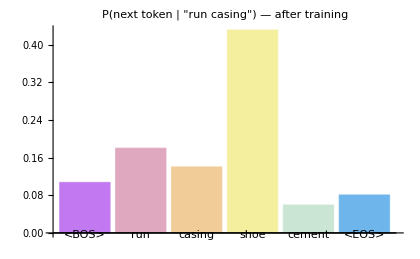

```mathematica
BarChart[probabilitiesNew, ChartLabels -> Vocabulary, ChartStyle -> "Pastel",
  PlotLabel -> "P(next token | \"run casing\") — after training", ImageSize -> 420]
```

## 15. What Just Happened?

The forward pass turned "run casing" into a full probability distribution over the vocabulary (Sections 2-10).

We told the model the correct next token was "shoe", and cross-entropy loss measured exactly how wrong its distribution was (Section 11).

The gradient measured how each parameter of WOut would affect that loss if nudged (Section 12), and we checked that gradient numerically rather than taking it on faith.

Gradient descent moved every weight a small step opposite its gradient (Section 13).

Running the identical input, "run casing", through the updated weights produced a different, better distribution: higher P("shoe"), lower loss (Section 14).

That loop — predict, measure error, compute gradient, update weights, predict again — is the numerical core of how transformer language models learn. Real training repeats it millions or billions of times, over enormous datasets, updating every parameter in the network (not just an output projection), with additional machinery (Section 16) layered on top. This notebook does not claim that a single hand-worked update on one example captures everything about training a real model — only that the arithmetic at the heart of it is exactly this.

## 16. Scale Comparison

```mathematica
Grid[{
   {"", "Toy model (this notebook)", "A modern pretrained language model"},
   {"Vocabulary size", "~6 tokens", "tens of thousands to ~1,000,000+ tokens"},
   {"Embedding dimension", "2", "hundreds to tens of thousands"},
   {"Attention heads", "1", "dozens, run in parallel per layer"},
   {"Transformer blocks", "1", "dozens to over 100, stacked"},
   {"Parameters", "tens", "billions, sometimes hundreds of billions"},
   {"Training examples", "1", "trillions of tokens"},
   {"Training updates", "1 (shown by hand)", "millions to billions"}
   }, Frame -> All, Background -> {None, {LightGray, None}}, Dividers -> All]
```

| Toy model (this notebook) | A modern pretrained language model
Vocabulary size | ~6 tokens | tens of thousands to ~1,000,000+ tokens
Embedding dimension | 2 | hundreds to tens of thousands
Attention heads | 1 | dozens, run in parallel per layer
Transformer blocks | 1 | dozens to over 100, stacked
Parameters | tens | billions, sometimes hundreds of billions
Training examples | 1 | trillions of tokens
Training updates | 1 (shown by hand) | millions to billions

The arithmetic did not suddenly become magic. The scale became enormous. Every quantity in the right-hand column is produced by the same handful of operations used above — matrix multiplication, softmax, cross-entropy, gradients, gradient descent — repeated over far more parameters, far more data, and far more training steps, and (per Section 16's introduction and Section "What we left out" above) combined with additional architectural components we deliberately omitted here: LayerNorm, residual connections, multi-head attention, larger feed-forward networks, positional encodings, and more. A real system is not simply this exact toy multiplied larger — it is this mechanism plus those additional pieces, at a scale where hand computation is impossible and was never the goal.

## Interactive: What Happens If I Change This Number?

The three controls below let you perturb the trained model along three different axes: the learning rate used for the update, one specific output weight (WOut[[1,4]], the weight from h's first coordinate into "shoe"'s logit, before any training update is applied), and one specific embedding coordinate (the second coordinate of "casing"'s embedding, which feeds directly into X, Q, K, V, and everything downstream). Moving any slider recomputes the entire forward pass from scratch and redraws the attention weights, the next-token probability bar chart, P("shoe"), and the loss.

```mathematica
Manipulate[
  Module[{emb, xLoc, qLoc, kLoc, vLoc, rawLoc, scaledLoc, maskedLoc, attnLoc,
    attnOutLoc, hLoc, wOutLoc, logitsLoc, probsLoc, pShoeLoc, lossLoc},
   emb = EmbeddingMatrix;
   emb[[3, 2]] = casingCoord2;
   xLoc = emb[[tokenIDs]];
   qLoc = xLoc.WQ; kLoc = xLoc.WK; vLoc = xLoc.WV;
   rawLoc = qLoc.Transpose[kLoc];
   scaledLoc = N[rawLoc/Sqrt[2]];
   maskedLoc = {{scaledLoc[[1, 1]], -Infinity}, {scaledLoc[[2, 1]], scaledLoc[[2, 2]]}};
   attnLoc = SoftmaxRow /@ maskedLoc;
   attnOutLoc = attnLoc.vLoc;
   hLoc = attnOutLoc[[2]];
   wOutLoc = WOut;
   wOutLoc[[1, 4]] = wOut14;
   logitsLoc = hLoc.wOutLoc;
   probsLoc = Softmax2[logitsLoc];
   pShoeLoc = probsLoc[[targetIndex]];
   lossLoc = -Log[pShoeLoc];
   Column[{
     Grid[{{"attention weights (row 2, \"casing\")",
        NumberForm[attnLoc[[2]], {4, 3}]}}],
     BarChart[probsLoc, ChartLabels -> Vocabulary, ChartStyle -> "Pastel",
      PlotRange -> {0, 1}, ImageSize -> 380],
     Grid[{
       {"P(\"shoe\")", NumberForm[pShoeLoc, {5, 4}]},
       {"Loss", NumberForm[lossLoc, {5, 4}]}
       }, Frame -> All]
     }]
   ],
  {{learningRateM, 2, "learning rate (unused above, shown for Section 13 intuition)"}, 0, 4, 0.1},
  {{wOut14, 1, "WOut[[1,4]]  (weight feeding \"shoe\"'s logit)"}, -3, 3, 0.1},
  {{casingCoord2, 1, "casing embedding, 2nd coordinate"}, -2, 2, 0.1}
  ]
```

Try pushing wOut14 higher: P("shoe") should rise, and the loss should fall, mirroring exactly what one gradient step did automatically in Sections 12-14. Try moving the casing embedding coordinate away from its original value of 1: because "casing"'s embedding feeds X, Q, K, V, and the attention weights, this single number reaches every stage of the computation, not just the last one.

## Try It Without Mathematica

Everything below can be reproduced with paper, a pencil, and a calculator with e^x and ln buttons. All of the given values below were introduced earlier in this notebook — nothing here is new.

### Given

Vocabulary (token : ID)
  <BOS>:1   run:2   casing:3   shoe:4   cement:5   <EOS>:6

Input tokens: "run", "casing"  ->  token IDs {2, 3}
Target token: "shoe"  ->  token ID 4

Embeddings (token -> vector):
  run    -> (1, 0)
  casing -> (0, 1)

X = | 1  0 |        WQ = | 1  0 |     WK = | 1  1 |     WV = | 1  0 |
    | 0  1 |             | 1  1 |          | 0  1 |          | 0  1 |

WOut = |  0   1   0   1  -1   0 |
       |  0   0   1  -1   0  -1 |
      (columns, in order: <BOS>, run, casing, shoe, cement, <EOS>)

d (embedding dimension, for scaling) = 2
Learning rate = 2

### Fill in the blanks

Q = ______              K = ______              V = ______

Q . Transpose[K] = ______

Scaled scores  =  (Q . Transpose[K]) / Sqrt[2]  =  ______

Masked scores (position 1 cannot see position 2; replace that entry with -∞) = ______

Attention probabilities (softmax each row of the masked scores) = ______

Attention output = Attention probabilities . V = ______
  (take row 2 of this — call it h — this is what predicts the token after "casing")

Logits = h . WOut = ______   (6 numbers, one per vocabulary token)

Softmax the logits  ->  Probabilities = ______

P("shoe") = ______   (the probability entry for token 4)

Loss = -Log[ P("shoe") ] = ______

Check your work against Sections 4, 5, 6, 7, 8, 9, 10, and 11 above, which compute exactly these quantities and display every intermediate step. HAND_CALCULATION.md (in this project folder) reproduces this same worksheet as a plain-text file you can print.

## Appendix A: Automated Verification

Before trusting any of the numbers above, we check them programmatically: every matrix has the dimensions it should, every softmax row sums to 1, the causal mask actually zeroes out the disallowed attention weight, the target probability is pulled from the correct index, cross-entropy is computed correctly, the gradient has the right shape and the right sign, the updated weights are actually different from the old ones and are actually used for the second forward pass, and — the two claims this whole notebook depends on — P("shoe") increases and the loss decreases after the one training step. This cell loads TinyTransformerByHand.wl (the standalone reference implementation shipped alongside this notebook) and runs its full check suite.

```mathematica
notebookDir = Quiet[NotebookDirectory[]];
If[! StringQ[notebookDir], notebookDir = Directory[]];
SetDirectory[notebookDir];
Quiet[Get["TinyTransformerByHand.wl"], {General::shdw}];
TinyTransformerByHand`RunAllChecks[];
```

=== TinyTransformerByHand verification ===

[PASS] X is 2x2

[PASS] Q is 2x2

[PASS] K is 2x2

[PASS] V is 2x2

[PASS] Attention weights are 2x2

[PASS] Attention output is 2x2

[PASS] h is length 2

[PASS] Logits is length 6

[PASS] Probabilities is length 6

[PASS] dLogits is length 6

[PASS] dWOut is 2x6

[PASS] Attention row 1 sums to 1

[PASS] Attention row 2 sums to 1

[PASS] Output probabilities sum to 1

[PASS] Causal mask: position 1 cannot see position 2

[PASS] Causal mask: position 2 CAN see position 1

[PASS] Target index points to "shoe"

[PASS] P(shoe) equals Probabilities[[TargetIndex]]

[PASS] Loss equals -Log[P(shoe)]

[PASS] Loss is positive

[PASS] dLogits sums to ~0

[PASS] dLogits is negative only at the target index

[PASS] Update formula matches W - lr*grad

[PASS] Updated weights actually differ from old weights

[PASS] Updated model actually uses updated WOut (logits changed)

[PASS] P(shoe) increases after the update

[PASS] Loss decreases after the update

ALL CHECKS PASSED (27 checks)

## Appendix B: Optional Cross-Check With a Built-In Function

As a final, optional sanity check — and only as a cross-check, never as a replacement for the manual derivation above — we compare our hand-written softmax against Mathematica's built-in Softmax function applied to the same logits. This notebook does not use NetChain, NetGraph, NetTrain, Predict, or Classify anywhere; Softmax here is an ordinary numeric function, not a neural-network abstraction, and we use it only to confirm agreement with Sections 7 and 10, not to compute anything new.

```mathematica
builtInProbabilities = Softmax[logits];
{"our manual softmax" -> N[probabilities, 6], "built-in Softmax[]" -> N[builtInProbabilities, 6],
  "agree?" -> Max[Abs[probabilities - builtInProbabilities]] < 10^-10}
```

{our manual softmax→{0.143268,0.279913,0.199329,0.201188,0.0733289,0.102974},built-in Softmax[]→{0.143268,0.279913,0.199329,0.201188,0.0733289,0.102974},agree?→True}